```mathematica
Remove["Global`*"];
fd=((2/L)*(1-(d/L)));
fr = ((4*r)/ ((π *Da^2)/4))*ArcCos[r/Da] - ((2 * (r^2))/ (π * ((Da^3)/8)))*Sqrt[1 - ((r^2)/ (Da^2))];

a={d∈Reals,r∈Reals,w∈Reals,Da∈Reals,L∈Reals, L>Da>w>0,w>r>0, w>d>0};
```

```mathematica
CDF1=FullSimplify[Integrate[fd*fr,{r,0,w},{d,0,Sqrt[w^2-r^2]},Assumptions->a],a]
```

1/(90 Da^4 L^2 π)(15 (-3 Da^4 w √((Da-w) (Da+w))+8 w^5 √((Da-w) (Da+w))+2 Da^2 w^3 (16 L π+5 √((Da-w) (Da+w)))-24 Da^2 w^4 ArcCos[w/Da]+3 Da^4 (Da^2-4 w^2) ArcSin[w/Da])+128 Da L ((2 Da^4-7 Da^2 w^2-3 w^4) EllipticE[w^2/Da^2]-2 (Da^4-4 Da^2 w^2+3 w^4) EllipticK[w^2/Da^2]))

```mathematica
PDF1=FullSimplify[Dt[CDF1,w,Constants -> {L, Da}],a]
```

1/(3 Da^4 L^2 π)4 w (3 Da^2 w √((Da-w) (Da+w))+6 w^3 √((Da-w) (Da+w))+12 Da^2 w (L π-w ArcCos[w/Da])-3 Da^4 ArcSin[w/Da]+16 Da L (-(Da^2+w^2) EllipticE[w^2/Da^2]+(Da-w) (Da+w) EllipticK[w^2/Da^2]))

```mathematica
(* we need an integration constant for CDF2. we find the limit of CDF1 as w->Da and use this as the integration constant*)
(* We also use it to plug the hole created by the fact CDF1 and CDF2 dont exist at Da *)
K1[w_]=(1/(90*Da^4*L^2*Pi))*(15*(-3*Da^4*w*Sqrt[(Da - w)*(Da + w)] + 
     8*w^5*Sqrt[(Da - w)*(Da + w)] + 2*Da^2*w^3*
      (16*L*Pi + 5*Sqrt[(Da - w)*(Da + w)]) - 24*Da^2*w^4*ArcCos[w/Da] + 
     3*Da^4*(Da^2 - 4*w^2)*ArcSin[w/Da]) + 
   128*Da*L*((2*Da^4 - 7*Da^2*w^2 - 3*w^4)*EllipticE[w^2/Da^2]));
K1 = FullSimplify[K1[Da]]
```

(Da (-135 Da π+64 L (-32+15 π)))/(180 L^2 π)

```mathematica
(* Calculate the limit of PDF1 at Da so we can plug the hole created by the fact PDF1 and PDF2 dont exist at Da *)
```

```mathematica
K2[w_]=(1/(3*Da^4*L^2*Pi))*4*w*(3*Da^2*w*Sqrt[(Da - w)*(Da + w)] + 
   6*w^3*Sqrt[(Da - w)*(Da + w)] + 12*Da^2*w*(L*Pi - w*ArcCos[w/Da]) - 
   3*Da^4*ArcSin[w/Da] + 16*Da*L*((-(Da^2 + w^2))*EllipticE[w^2/Da^2]));
K2 = FullSimplify[K2[Da]]
```

(2 (-3 Da π+8 L (-8+3 π)))/(3 L^2 π)

```mathematica
b ={d∈Reals,r∈Reals,w∈Reals,Da∈Reals,L∈Reals,L>Da,L>w>Da>0, w>r>0,w>d>0};
```

```mathematica
CDF2=FullSimplify[Integrate[fd*fr,{r,0,Da},{d,Sqrt[Da^2-r^2],Sqrt[w^2-r^2]},Assumptions->b] + K1,b]
```

(15 Da^2 π (3 Da^4-12 Da^2 w^2+64 L w^3)+256 L w ((2 Da^4-7 Da^2 w^2-3 w^4) EllipticE[Da^2/w^2]-(Da^4+2 Da^2 w^2-3 w^4) EllipticK[Da^2/w^2]))/(180 Da^4 L^2 π)

```mathematica
PDF2=FullSimplify[Dt[CDF2,w,Constants -> {L, Da}],b]
```

-(2 w (3 Da^2 π (Da^2-8 L w)+32 L w ((Da^2+w^2) EllipticE[Da^2/w^2]+(Da-w) (Da+w) EllipticK[Da^2/w^2])))/(3 Da^4 L^2 π)

```mathematica
c = {d∈Reals,r∈Reals,w∈Reals,Da∈Reals,L∈Reals,w>L>d>Da>r>0,w>Sqrt[w^2-L^2],Da>Sqrt[w^2-L^2],L>0, w > 0};
```

```mathematica
CDF3 = FullSimplify[CDF2 -FullSimplify[Integrate[fd*fr,{r, 0, Sqrt[w^2-L^2]} ,{d, L,Sqrt[w^2-r^2]},Assumptions->c],c]]
```

(45 Da^6 (-L^2+w^2)-24 (L-w)^2 (L+w)^2 (L^2-5 w^2) (L^2+w^2)+2 Da^2 (L-w) (L+w) (29 L^2-5 w^2) (L^2+3 w^2)+Da^4 (37 L^4-195 w^4+2 L^2 (79 w^2+45 π √(-(L-w) (L+w) (Da^2+L^2-w^2))))-15 Da^2 √(-(L-w) (L+w) (Da^2+L^2-w^2)) (-3 Da^4+12 Da^2 (L^2+w^2)+8 (L^4-6 L^2 w^2-3 w^4)) ArcSec[Da/(√(-L^2+w^2))]-128 L w √(-(L-w) (L+w) (Da^2+L^2-w^2)) ((-2 Da^4+7 Da^2 w^2+3 w^4) EllipticE[Da^2/w^2]+(2 Da^4-7 Da^2 w^2-3 w^4) EllipticE[ArcCsc[Da/(√(-L^2+w^2))],Da^2/w^2]-2 Da w^3 EllipticF[ArcCos[L/w],w^2/Da^2]-Da^4 EllipticF[ArcCsc[Da/(√(-L^2+w^2))],Da^2/w^2]+3 w^4 EllipticF[ArcCsc[Da/(√(-L^2+w^2))],Da^2/w^2]+(Da^4+2 Da^2 w^2-3 w^4) EllipticK[Da^2/w^2]))/(90 Da^4 L^2 π √(-(L-w) (L+w) (Da^2+L^2-w^2)))

```mathematica
(*PDF3=FullSimplify[ Dt[CDF3,w,Constants -> {L, Da}],c]*)
PDF3 = FullSimplify[PDF2 -FullSimplify[ Dt[Integrate[Integrate[fd*fr,{d, L, Sqrt[w^2-r^2]},Assumptions->c],{r, 0, Sqrt[w^2-L^2]},Assumptions->c],w,Constants -> {L, Da}],c]]
```

1/(3 Da^4 L^2 π)4 w (-√(-(L-w) (L+w) (Da^2+L^2-w^2)) (3 Da^2+2 L^2+6 w^2)-3 Da^2 (Da^2-4 (L^2+w^2)) ArcSec[Da/(√(-L^2+w^2))]+16 L w (-(Da^2+w^2) EllipticE[Da^2/w^2]+(Da^2+w^2) EllipticE[ArcCsc[Da/(√(-L^2+w^2))],Da^2/w^2]+(Da-w) (Da+w) (EllipticF[ArcCsc[Da/(√(-L^2+w^2))],Da^2/w^2]-EllipticK[Da^2/w^2])))

```mathematica
CForm[PDF1]
```

(4*w*(3*Power(Da,2)*w*Sqrt((Da - w)*(Da + w)) + 6*Power(w,3)*Sqrt((Da - w)*(Da + w)) + 
       12*Power(Da,2)*w*(L*Pi - w*ArcCos(w/Da)) - 3*Power(Da,4)*ArcSin(w/Da) + 
       16*Da*L*(-((Power(Da,2) + Power(w,2))*EllipticE(Power(w,2)/Power(Da,2))) + 
          (Da - w)*(Da + w)*EllipticK(Power(w,2)/Power(Da,2)))))/
   (3.*Power(Da,4)*Power(L,2)*Pi)

```mathematica
CForm[PDF2]
```

(-2*w*(3*Power(Da,2)*Pi*(Power(Da,2) - 8*L*w) + 
       32*L*w*((Power(Da,2) + Power(w,2))*EllipticE(Power(Da,2)/Power(w,2)) + 
          (Da - w)*(Da + w)*EllipticK(Power(Da,2)/Power(w,2)))))/
   (3.*Power(Da,4)*Power(L,2)*Pi)

```mathematica
CForm[PDF3]
```

(4*w*(-(Sqrt(-((L - w)*(L + w)*(Power(Da,2) + Power(L,2) - Power(w,2))))*
          (3*Power(Da,2) + 2*Power(L,2) + 6*Power(w,2))) - 
       3*Power(Da,2)*(Power(Da,2) - 4*(Power(L,2) + Power(w,2)))*
        ArcSec(Da/Sqrt(-Power(L,2) + Power(w,2))) + 
       16*L*w*(-((Power(Da,2) + Power(w,2))*EllipticE(Power(Da,2)/Power(w,2))) + 
          (Power(Da,2) + Power(w,2))*
           EllipticE(ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))),Power(Da,2)/Power(w,2)) + 
          (Da - w)*(Da + w)*(EllipticF(ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))),
              Power(Da,2)/Power(w,2)) - EllipticK(Power(Da,2)/Power(w,2))))))/
   (3.*Power(Da,4)*Power(L,2)*Pi)

```mathematica
CForm[CDF1]
```

(15*(-3*Power(Da,4)*w*Sqrt((Da - w)*(Da + w)) + 8*Power(w,5)*Sqrt((Da - w)*(Da + w)) + 
        2*Power(Da,2)*Power(w,3)*(16*L*Pi + 5*Sqrt((Da - w)*(Da + w))) - 
        24*Power(Da,2)*Power(w,4)*ArcCos(w/Da) + 
        3*Power(Da,4)*(Power(Da,2) - 4*Power(w,2))*ArcSin(w/Da)) + 
     128*Da*L*((2*Power(Da,4) - 7*Power(Da,2)*Power(w,2) - 3*Power(w,4))*
         EllipticE(Power(w,2)/Power(Da,2)) - 
        2*(Power(Da,4) - 4*Power(Da,2)*Power(w,2) + 3*Power(w,4))*
         EllipticK(Power(w,2)/Power(Da,2))))/(90.*Power(Da,4)*Power(L,2)*Pi)

```mathematica
CForm[CDF2]
```

(15*Power(Da,2)*Pi*(3*Power(Da,4) - 12*Power(Da,2)*Power(w,2) + 64*L*Power(w,3)) + 
     256*L*w*((2*Power(Da,4) - 7*Power(Da,2)*Power(w,2) - 3*Power(w,4))*
         EllipticE(Power(Da,2)/Power(w,2)) - 
        (Power(Da,4) + 2*Power(Da,2)*Power(w,2) - 3*Power(w,4))*
         EllipticK(Power(Da,2)/Power(w,2))))/(180.*Power(Da,4)*Power(L,2)*Pi)

```mathematica
CForm[CDF3]
```

(45*Power(Da,6)*(-Power(L,2) + Power(w,2)) - 
     24*Power(L - w,2)*Power(L + w,2)*(Power(L,2) - 5*Power(w,2))*
      (Power(L,2) + Power(w,2)) + 2*Power(Da,2)*(L - w)*(L + w)*
      (29*Power(L,2) - 5*Power(w,2))*(Power(L,2) + 3*Power(w,2)) + 
     Power(Da,4)*(37*Power(L,4) - 195*Power(w,4) + 
        2*Power(L,2)*(79*Power(w,2) + 
           45*Pi*Sqrt(-((L - w)*(L + w)*(Power(Da,2) + Power(L,2) - Power(w,2)))))) - 
     15*Power(Da,2)*Sqrt(-((L - w)*(L + w)*(Power(Da,2) + Power(L,2) - Power(w,2))))*
      (-3*Power(Da,4) + 12*Power(Da,2)*(Power(L,2) + Power(w,2)) + 
        8*(Power(L,4) - 6*Power(L,2)*Power(w,2) - 3*Power(w,4)))*
      ArcSec(Da/Sqrt(-Power(L,2) + Power(w,2))) - 
     128*L*w*Sqrt(-((L - w)*(L + w)*(Power(Da,2) + Power(L,2) - Power(w,2))))*
      ((-2*Power(Da,4) + 7*Power(Da,2)*Power(w,2) + 3*Power(w,4))*
         EllipticE(Power(Da,2)/Power(w,2)) + 
        (2*Power(Da,4) - 7*Power(Da,2)*Power(w,2) - 3*Power(w,4))*
         EllipticE(ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))),Power(Da,2)/Power(w,2)) - 
        2*Da*Power(w,3)*EllipticF(ArcCos(L/w),Power(w,2)/Power(Da,2)) - 
        Power(Da,4)*EllipticF(ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))),
          Power(Da,2)/Power(w,2)) + 3*Power(w,4)*
         EllipticF(ArcCsc(Da/Sqrt(-Power(L,2) + Power(w,2))),Power(Da,2)/Power(w,2)) + 
        (Power(Da,4) + 2*Power(Da,2)*Power(w,2) - 3*Power(w,4))*
         EllipticK(Power(Da,2)/Power(w,2))))/
   (90.*Power(Da,4)*Power(L,2)*Pi*Sqrt(-((L - w)*(L + w)*
         (Power(Da,2) + Power(L,2) - Power(w,2)))))

```mathematica
CForm[K1]
```

(Da*(-135*Da*Pi + 64*L*(-32 + 15*Pi)))/(180.*Power(L,2)*Pi)

```mathematica
CForm[K2]
```

(2*(-3*Da*Pi + 8*L*(-8 + 3*Pi)))/(3.*Power(L,2)*Pi)

0.5

2

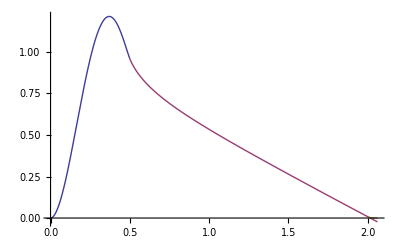

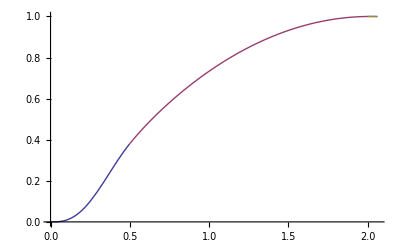

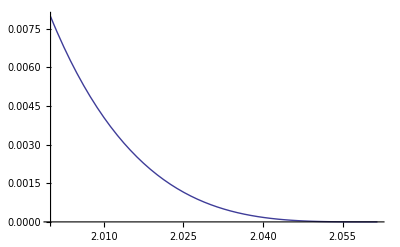

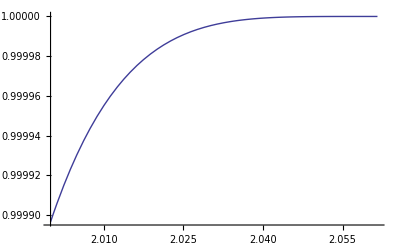

```mathematica
Da=0.5
L=2
Plot[{PDF1,PDF2,PDF3},{w,0,Sqrt[L^2+Da^2]}]
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+Da^2]}]
Plot[{PDF3}, {w,L,Sqrt[L^2+Da^2]}]
Plot[{CDF3}, {w,L,Sqrt[L^2+Da^2]}]
```

1

2

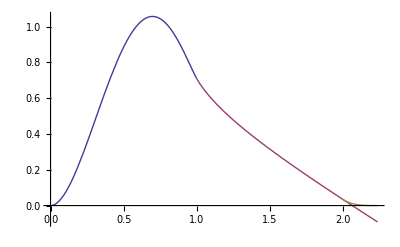

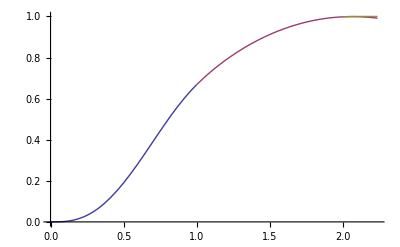

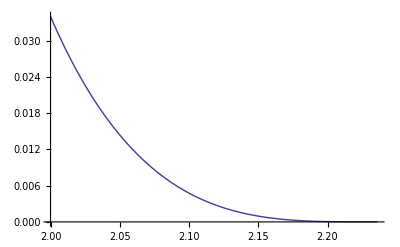

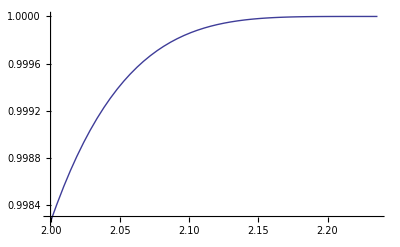

```mathematica
Da=1
L=2
Plot[{PDF1,PDF2,PDF3},{w,0,Sqrt[L^2+Da^2]}]
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+Da^2]}]
Plot[{PDF3}, {w,L,Sqrt[L^2+Da^2]}]
Plot[{CDF3}, {w,L,Sqrt[L^2+Da^2]}]
```

1

10

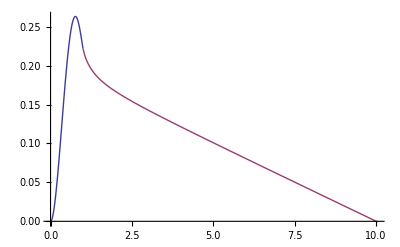

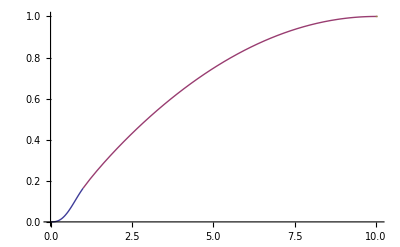

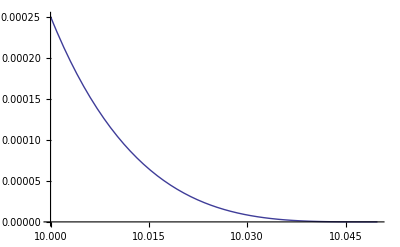

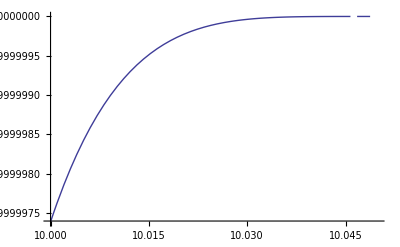

```mathematica
Da=1
L=10
Plot[{PDF1,PDF2,PDF3},{w,0,Sqrt[L^2+Da^2]}]
Plot[{CDF1,CDF2,CDF3},{w,0,Sqrt[L^2+Da^2]}]
Plot[{PDF3}, {w,L,Sqrt[L^2+Da^2]}]
Plot[{CDF3}, {w,L,Sqrt[L^2+Da^2]}]
```